### Naloga 1

V Mathematici predstavimo daljico v obliki Daljica [AA_, BB_], kjer sta AA in BB točki predstavljeni s parom koordinat v obliki {x, y}. Primer:

```mathematica
d = Daljica[{-1,1},{3,-1}];
```

Sestavi naslednje funkcije:

Dolzina [ Daljica [AA_, BB_]], ki vrne dolžino daljice.

```mathematica
Dolzina[Daljica[AA_, BB_]] := Norm[BB - AA]
```

```mathematica
Dolzina[d]
```

2 √5

EnacbaNosilke [ Daljica [AA_, BB_]], ki vrne enačbo premice nosilke daljice. Primer za daljico d kot zgoraj je enačba nosilke y = -x/2 + 1/2.

```mathematica
EnacbaNosilke[Daljica[AA_,BB_]] := Module[{x1, y1, x2, y2, k, n},
{x1, y1}=AA;
{x2, y2}=BB;
k = (y2 - y1)/(x2 - x1);
n =n /.First[Solve[y1 == k*x1 + n, n]];
y ==  k*x + n
]
```

```mathematica
EnacbaNosilke[d]
```

y==1/2-x/2

Slika [ Daljica [AA_, BB_]], ki vrne grefični objekt Line, ki predstavlja daljico.

```mathematica
Slika[Daljica[AA_,BB_]] := Line[{AA, BB}]
```

```mathematica
Slika[d]
```

Line[{{-1,1},{3,-1}}]

Nrisi [ d__Daljica], ki za eno ali več podanih daljic le-te izriše.

```mathematica
Narisi[d_Daljica] := Graphics[Slika[d]]
Narisi[d__Daljica] := Graphics[Map[Slika, List[d]]]
```

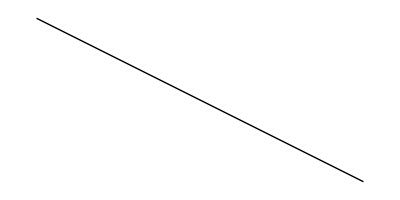

```mathematica
Narisi[d]
```

### Naloga 2

Sestavi funkcijo Presek [ Daljica [AA_, BB_], Daljica [CC_, DD_]], ki vrne presečišče daljic, če se sekata, oziroma prazen seznam ({}).

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]]:= Module[{resitev},
resitev = Solve[{AA + r(BB - AA) == CC + s(DD - CC), r ≥ 0, r ≤ 1, s ≥ 0, s ≤ 1}, {r, s}];
If[resitev == {},
{},
First[AA + r(BB - AA) /. resitev]
]
]
```

```mathematica
d2 = Daljica[{-1, -1}, {3, 1}];
d3 = Daljica[{-1, 2}, {3, 0}];
```

```mathematica
Presek[d, d2]
```

{1,0}

```mathematica
Presek[d, d3]
```

{}

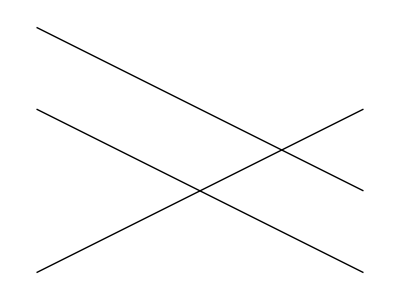

```mathematica
Narisi[d, d2, d3]
```

### Naloga 3

Sklenjen mnogokotnik podamo v obliki seznama z glavo Mnogokotnik. Primer:

```mathematica
m1 = Mnogokotnik[{0, 0}, {1, 1}, {0, 3}, {-1, 2}];
```

Ker gre za sklenjen mnogokotnik, predvidevamo, da ima ta povezave med zaporednimi točkami ter od zadnje do prve točke. Sestavi naslednje funkcije:

Slika [ Mnogokotnik [t__]], ki predstavi mnogokotnik s pomočjo graﬁčnega objekta Line. Najprej sestavi nov seznam točk, ki vključuje obstoječe točke mnogokotnika ter še ponovljeno prvo. Pozor: pazi, da ne izbrišeš obstoječe funkcije za sliko daljice!

```mathematica
ClearAll [Slika, Narisi]
```

```mathematica
Slika[Mnogokotnik[t__]] := Line[{t}]
```

```mathematica
Slika[m1]
```

Line[{{0,0},{1,1},{0,3},{-1,2}}]

Narisi [ m__Mnogokotnik], ki nariše enega ali več mnogokotnikov. Pazi,pri risanju moraš narediti tudi daljico od zadnje do začetne točke. Premisli, kako iz obstoječega seznama točk sestaviš nov seznam, ki je daljši za eno točko, t.j. ponovljeno prvo točko (Namig: funkciji Append ter First na seznamih.)

```mathematica
ClearAll[Slika2, m, Narisi]
```

```mathematica
m = Append[m1, m1[[1]]];
Narisi[m__Mnogokotnik] := Graphics[Map[Slika, List[m]]]
```

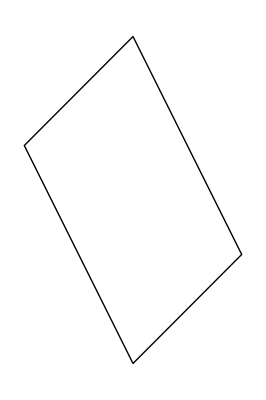

```mathematica
Narisi[m]
```

PravilniNKotnik [n_, r_ ], ki nariše pravilni n-kotnik s središčem v točki (0, 0) in s točkami na krožnici z radijem r, pri čemer je ena točka v (r, 0). Namig: uporabi funkcijo Table in upoštevaj, da se točke nahajajo na koordinatah (r*cos(2π / n) ,r*sin(2π / n)) za i =0,...,n−1. Izriši

```mathematica
ClearAll[Narisi, i, n, r, p5]
```

```mathematica
p5 = PravilniNKotnik[5, 2];
```

```mathematica
Narisi[p5__PravilniNKotnik] := Graphics[{
	Line[
		Table[{p5[[2]] * Cos[(2*Pi * i) / p5[[1]]],
		p5[[2]] * Sin[(2*Pi * i) / p5[[1]]]}, {i, 0, p5[[1]]}]]}]
```

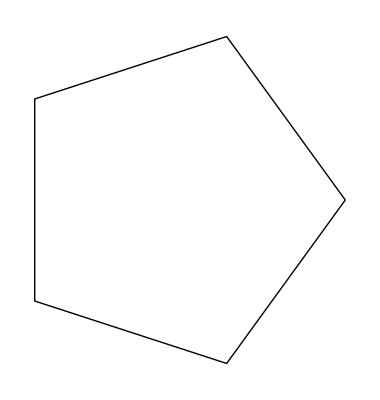

```mathematica
Narisi[p5]
```

Nadgradi prejšnjo funkcijo v PravilniNKotnik[n_, r_, phi_], ki zgornji pravilni n-kotnik zavrti za kot phi. Premisli, kako je treba nadgraditi formulo za posamezno točko, da se premakne za kot phi. Rezultat uporabi v kombinaciji s funkcijo Manipulate in interaktivno demonstriraj rotacijo.

```mathematica
p = PravilniNKotnik[5, 2, 2Pi];
```

```mathematica
Zavrti[p__PravilniNKotnik] := Manipulate[Graphics[{
	Line[
		Table[{p[[2]] * Cos[((2*Pi * i) / p[[1]]) + fi],
		 p[[2]] * Sin[((2*Pi * i) / p[[1]]) + fi]}, {i, 0, p[[1]]}]]}], 
			{fi, 0, p[[3]]}]
```

```mathematica
Zavrti[p]
```

Daljice[Mnogokotnik[t__]], ki vrne seznam daljic, ki tvorijo mnogokotnik. Uporabi funkcijo Partition. V dokumentaciji preveri, kako deluje funkcija ter kako se uporablja zamikanje. Oglej si, kaj naredita naslednja ukaza: Partition[{1, 2, 3, 4, 5} , 2], Partition[{1, 2, 3, 4, 5} , 2, 1]

```mathematica
m1 = Mnogokotnik[{0, 0}, {1, 1}, {0, 3}, {-1, 2}];
m = Append[m1, m1[[1]]];
```

```mathematica
Daljice[Mnogokotnik[t__]] := Partition[{t}, 2, 1]
```

```mathematica
Daljice[m]
```

{{{0,0},{1,1}},{{1,1},{0,3}},{{0,3},{-1,2}},{{-1,2},{0,0}}}

### Naloga 4

Sestavi funkcijo Presek[m_Mnogokotnik, d_Daljica], ki izračuna presečišča mnogokotnika in daljice. Pri tem uporabi že napisane funkcije ter pazi, da rezultat ne vrne istih presečišč večkrat. Poskusi uporabiti vgrajeni funkciji Select in DeleteDuplicates. Pomagaj si z naslednjimi primeri. Funkcijo lahko deﬁniramo tudi na naslednji način (namesto argumenta damo znak #, na koncu deﬁnicije pa dodamo znak &.

```mathematica
ClearAll[d1, m1, m, Presek2, Presek1, t, Presek, sez]
```

```mathematica
d1 = Daljica[{-1,1},{3,-1}];
m1 = Mnogokotnik[{0, 0}, {1, 1}, {0, 3}, {-1, 2}];
m = Append[m1, m1[[1]]];
```

```mathematica
PresekVec[m_Mnogokotnik, d_Daljica] := 
	For[i = 1, i ≤ Length[Daljice[m]] , i++,
		Print[Presek[Daljica[Daljice[m][[i]][[1]], Daljice[m][[i]][[2]]], d]]]
```

```mathematica
PresekVec[m, d1]
```

{1/3,1/3}

{}

{}

{-1/3,2/3}

```mathematica
aliJePrazen = Length[#] > 0 &;
```

```mathematica
Select[{{1/3, 1/3}, {}, {}, {-1/3, 2/3}}, aliJePrazen]
```

{{1/3,1/3},{-1/3,2/3}}

### Naloga 5

Spodnja funkcija izračuna (uporabi) funkcijo f na vseh parih iz dveh seznamov.

```mathematica
VsiPari[f_, sez1_, sez2_] := Flatten[Outer[f, sez1, sez2], 1]
```

```mathematica
VsiPari[f, {1, 2, 3}, {a, b}]
```

{f[1,a],f[1,b],f[2,a],f[2,b],f[3,a],f[3,b]}

Preuči, kaj točno naredita funkciji Outer in Flatten. Poglej v pomoč in preizkusi na primerih.

```mathematica
Outer[f,{a,b},{x,y,z}]
```

{{f[a,x],f[a,y],f[a,z]},{f[b,x],f[b,y],f[b,z]}}

Funkciji Outer podamo tri parametre. Prvi nam pove operacijo oziroma funkcijo s katero operiramo na ostalih dveh parametrih. Če so parametri seznami, funkcija izvaja dano opreacijo med vsemi elementi teh seznamov. (Npr. če je operacija množenje in želimo množiti med seboj dva seznama števil, kot rezultat dobimo sezname vseh možnih produktov med danima seznamoma.)

```mathematica
Flatten[{{a,b},{c,{j},e},{f,{g,h}}}]
Flatten[{{a,b},{c,{j},e},{f,{g,h}}}, 1]
```

{a,b,c,j,e,f,g,h}

{a,b,c,{j},e,f,{g,h}}

Funkcija Flatten iz danega seznama podseznamov ustvari en sam seznam. Funkciji lahko podamo še en parameter in sicer število, ki nam pove stopnjo podseznama iz katerih naredi en seznam ostale podsezname pa ohrani kot posezname seznama.

Sestavi funkcijo Presek[m1_Mnogokotnik, m2_Mnogokotnik], ki poišče presek dveh pravokotnikov. Uporabi funkcijo VsiPari.

```mathematica
ClearAll[Presek]
```

```mathematica
m1 = Mnogokotnik[{0, 0}, {1, 1}, {0, 3}, {-1, 2}];
m = Append[m1, m1[[1]]];
m2 = Mnogokotnik[{-2, 1}, {2, 1}, {2, -1}, {-2, -1}, {-2, 1}];
```

```mathematica
PresekVseh[m1_Mnogokotnik, m2_Mnogokotnik] := 
For[k = 1, k ≤ Length[Daljice[m2]], k++,
	For[i = 1, i ≤ Length[Daljice[m1]], i++,
		Print[Presek[Daljica[Daljice[m1][[i]][[1]], Daljice[m1][[i]][[2]]], 
		Daljica[Daljice[m2][[k]][[1]], Daljice[m2][[k]][[2]]]]]]]
```

```mathematica
PresekVseh[m, m2]
```

{1,1}

{1,1}

{}

{-1/2,1}

{}

{}

{}

«9 more identical outputs»

```mathematica
DeleteDuplicates[Select[{{1, 1}, {1, 1}, {}, {-1/2, 1}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}}, aliJePrazen]]
```

{{1,1},{-1/2,1}}

### Naloga 6

Izberi eno izmed nalog iz snovi pri linearni algebri in jo reši. Opiši potek in čim več računskega dela prepusti Mathematici. Če je možno, rezultate predstavi še graﬁčno.

```mathematica
n = Normala[2, 3, -1];
v = Vektor[2, 5, 1];
T = Točka[1, -3, 1];
```

```mathematica
x = 2a + 1;
y = 5a - 3;
z = a + 1;
```

```mathematica
Solve[2x + 3y + z == 14, a]
```

{{a→1}}

```mathematica
S = Točka[x, y, z]
```

Točka[3,2,2]